```mathematica
p={1,0}
m={0,1}
```

{1,0}

{0,1}

```mathematica
Table[p.PauliMatrix[i].m, {i, 3}]
```

{1,-ⅈ,0}

```mathematica
Table[m.PauliMatrix[i].p, {i, 3}]
```

{1,ⅈ,0}

```mathematica
Cross[%5,%6]
```

{0,0,2 ⅈ}

```mathematica
TensorProduct[p,p]
```

{{1,0},{0,0}}

```mathematica
states={{1,0,0,0}, {0,1,0,0},{0,0,1,0},{0,0,0,1}}
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
KroneckerProduct[PauliMatrix[3], PauliMatrix[2]]
```

{{0,-ⅈ,0,0},{ⅈ,0,0,0},{0,0,0,ⅈ},{0,0,-ⅈ,0}}

```mathematica
maEl[s1_,s2_]:=Table[s1.KroneckerProduct[PauliMatrix[3], PauliMatrix[i]].s2, {i, 3}]
num[plus_, state_]:=Cross[
maEl[plus, state],
maEl[state, plus]
]
Table[
num[{0,0,1,0}, s], {s, states[[{1,2,4}]]}
]
```

{{0,0,0},{0,0,0},{0,0,2 ⅈ}}

```mathematica
x/Sqrt[1-x^2]
```

x/(√(1-x^2))

```mathematica
Limit[%21,x->1]
```

Indeterminate

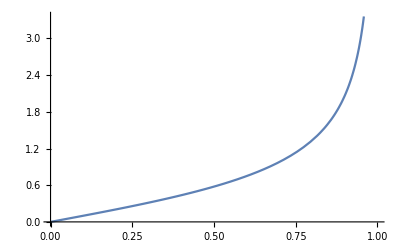

```mathematica
Plot[%21, {x, 0,1}]
```

```mathematica
expr=(y-qx L^2)/L
```

(-L^2 qx+y)/L

```mathematica
rule1={y->vf/vx y, qx->vx/vf (kx/γ +γ β (kz wpp - Engy)/vx), L->L vf Sqrt[γ/(vx vy)]}
```

{y→(vf y)/vx,qx→(vx (kx/γ+((-Engy+kz wpp) β γ)/vx))/vf,L→L vf √(γ/(vx vy))}

```mathematica
rule2={B->B vx vy /(vf^2 γ)}
```

{B→(B vx vy)/(vf^2 γ)}

```mathematica
expr/.rule1/.rule2//FullSimplify
```

(√(γ/(vx vy)) (vy y+L^2 (-kx vx+(Engy-kz wpp) β γ^2)))/(L γ)

```mathematica
%/.{vx->vf, vy->vf}//FullSimplify
```

(√(γ/vf^2) (vf y+L^2 (-kx vf+(Engy-kz wpp) β γ^2)))/(L γ)

```mathematica
Refine[%, vf∈PositiveReals]
```

(vf y+L^2 (-kx vf+(Engy-kz wpp) β γ^2))/(L vf √γ)

```mathematica
%/.γ->1/Sqrt[1-β^2]//FullSimplify
```

((1-β^2)^(1/4) (-kx L^2 vf+vf y+(L^2 (-Engy+kz wpp) β)/(-1+β^2)))/(L vf)

```mathematica
%/.{L->1, vf->1}
```

(1-β^2)^(1/4) (-kx+y+((-Engy+kz wpp) β)/(-1+β^2))

```mathematica
(1-β^2)^(1/4) (((-Engy+kz wpp) β)/(-1+β^2))
```

((-Engy+kz wpp) β (1-β^2)^(1/4))/(-1+β^2)

```mathematica
Simplify[((-Engy+kz wpp) β (1-β^2)^(1/4))/(-1+β^2)]
```

((Engy-kz wpp) β)/((1-β^2)^(3/4))

```mathematica
Expand[%70]
```

-kx L (1-β^2)^(1/4)+(y (1-β^2)^(1/4))/L-(Engy L β (1-β^2)^(1/4))/(vf (-1+β^2))+(kz L wpp β (1-β^2)^(1/4))/(vf (-1+β^2))

```mathematica
Expand[%69]
```

-(kx L)/(√γ)+y/(L √γ)+(Engy L β γ^(3/2))/vf-(kz L wpp β γ^(3/2))/vf

```mathematica
rules={qx->kx/γ + γ β (kz wpp - Engy)/vf, L->L Sqrt[γ]}
```

{qx→kx/γ+((-Engy+kz wpp) β γ)/vf,L→L √γ}

```mathematica
-I qy y - ((y-qx L^2)^2 + (y - (qx + qqx)L^2)^2)/(2 L^2)
```

-ⅈ qy y-((-L^2 qx+y)^2+(-L^2 (qqx+qx)+y)^2)/(2 L^2)

```mathematica
%/.rules
```

-ⅈ qy y-((y-L^2 γ (kx/γ+((-Engy+kz wpp) β γ)/vf))^2+(y-L^2 γ (qqx+kx/γ+((-Engy+kz wpp) β γ)/vf))^2)/(2 L^2 γ)

```mathematica
-ⅈ qy y-((y-L^2 γ (kx/γ+((-Engy+kz wpp) β γ)/vf))^2+(y-L^2 γ (qqx+kx/γ+((-Engy+kz wpp) β γ)/vf))^2)/(2 L^2 γ)
```

-ⅈ qy y-((y-L^2 γ (kx/γ+((-Engy+kz wpp) β γ)/vf))^2+(y-L^2 γ (qqx+kx/γ+((-Engy+kz wpp) β γ)/vf))^2)/(2 L^2 γ)

```mathematica
tmp=FullSimplify[%]
```

-ⅈ qy y-((-kx L^2+y+(L^2 (Engy-kz wpp) β γ^2)/vf)^2+(y-L^2 γ (qqx+kx/γ+((-Engy+kz wpp) β γ)/vf))^2)/(2 L^2 γ)

```mathematica
depress[poly_]:=depress[poly,First@Variables[poly]]

depress[poly_,x_]/;PolynomialQ[poly,x]:=Module[{n=Exponent[poly,x],x0},x0=-Coefficient[poly,x,n-1]/(n Coefficient[poly,x,n]);
Normal[Series[poly,{x,x0,n}]]]
```

```mathematica
depress[tmp, y]
```

1/4 (-L^2 qqx^2 γ+L^2 qy^2 γ)+1/2 ⅈ L^2 qy γ (-qqx+ⅈ qy-(2 kx)/γ+(2 Engy β γ)/vf-(2 kz wpp β γ)/vf)-((y+1/2 L^2 γ (-qqx+ⅈ qy-(2 kx)/γ+(2 Engy β γ)/vf-(2 kz wpp β γ)/vf))^2)/(L^2 γ)

```mathematica
yprime=(y+1/2 L^2 γ (-qqx+ⅈ qy-(2 kx)/γ+(2 Engy β γ)/vf-(2 kz wpp β γ)/vf))/(L Sqrt[γ])
```

(y+1/2 L^2 γ (-qqx+ⅈ qy-(2 kx)/γ+(2 Engy β γ)/vf-(2 kz wpp β γ)/vf))/(L √γ)

```mathematica
(y-qx L^2)/L/.rules/.y->L Sqrt[γ] y-1/2 L^2 γ (-qqx+ⅈ qy-(2 kx)/γ+(2 Engy β γ)/vf-(2 kz wpp β γ)/vf)
```

(L y √γ-1/2 L^2 γ (-qqx+ⅈ qy-(2 kx)/γ+(2 Engy β γ)/vf-(2 kz wpp β γ)/vf)-L^2 γ (kx/γ+((-Engy+kz wpp) β γ)/vf))/(L √γ)

```mathematica
y/L + L (I qy - qqx - 2 qx)/2/.rules
```

y/(L √γ)+1/2 L √γ (-qqx+ⅈ qy-2 (kx/γ+((-Engy+kz wpp) β γ)/vf))

```mathematica
FullSimplify[%]
```

y+1/2 L (qqx-ⅈ qy) √γ

```mathematica
(T=MatrixExp[1/2θ PauliMatrix[1]]//ExpToTrig)//MatrixForm
```

(Cosh[θ/2] | Sinh[θ/2]
Sinh[θ/2] | Cosh[θ/2])

```mathematica
(T.{a,b}).(T.{a,b})//FullSimplify
```

(a^2+b^2) Cosh[θ]+2 a b Sinh[θ]

```mathematica
{a,b}.(T/.θ->2 θ).{a,b}//FullSimplify
```

(a^2+b^2) Cosh[θ]+2 a b Sinh[θ]

```mathematica
Cosh[ArcTanh[x]]
```

1/(√(1-x^2))

```mathematica
Sinh[ArcTanh[x]]
```

x/(√(1-x^2))

```mathematica
T/.θ/2->-ArcTanh[tx]//MatrixForm
```

(1/(√(1-tx^2)) | -tx/(√(1-tx^2))
-tx/(√(1-tx^2)) | 1/(√(1-tx^2)))

# Here it begins

## Normal wave function

x and z plane wave part

```mathematica
phixz=Exp[I kx x] E[I kz z]/Sqrt[Lx Lz]
```

(ⅇ^(ⅈ kx x) ⅇ[ⅈ kz z])/(√(Lx Lz))

y part of function

```mathematica
phiy = Exp[-(y-kx L^2)^2/(2 L^2)]/Sqrt[α^2 + 1]{α/Sqrt[2^(M-1) (M-1)! √Pi L] HermiteH[M-1, (y-kx L^2)/L],
1/Sqrt[2^M M! √Pi L] HermiteH[M, (y-kx L^2)/L]}
```

{(ⅇ^(-((-kx L^2+y)^2)/(2 L^2)) α HermiteH[-1+M,(-kx L^2+y)/L])/(π^(1/4) √(1+α^2) √(2^(-1+M) L (-1+M)!)),(ⅇ^(-((-kx L^2+y)^2)/(2 L^2)) HermiteH[M,(-kx L^2+y)/L])/(π^(1/4) √(1+α^2) √(2^M L M!))}

```mathematica
alpharule=α->-Sqrt[2 e B ℏ M]/(E/vf - ℏ kz)
```

α→-(√2 √(B e M ℏ))/(ⅇ/vf-kz ℏ)

```mathematica
phi = phixz phiy;
```

```mathematica
phiy.phiy/.y-kx L^2 -> X L
```

(2^(1-M) ⅇ^(-X^2) α^2 HermiteH[-1+M,X]^2)/(L √π (1+α^2) (-1+M)!)+(2^-M ⅇ^(-X^2) HermiteH[M,X]^2)/(L √π (1+α^2) M!)

```mathematica
asumptions={{kx, y, kz}∈Reals,{ L,vf, B, e, ℏ}∈PositiveReals, M∈PositiveIntegers}
```

{(kx|y|kz)∈ℝ,(L|vf|B|e|ℏ)∈ℝ&&L>0&&vf>0&&B>0&&e>0&&ℏ>0,M∈ℤ&&M>0}

```mathematica
rules={qx->kx/γ + γ β (kz wpp - Engy)/vf, L->L Sqrt[γ]}
```

{qx→kx/γ+((-Engy+kz wpp) β γ)/vf,L→L √γ}

```mathematica
(phiy/.rules).(phiy/.rules)/.y-kx L^2 γ -> X L Sqrt[γ]
```

(2^(1-M) ⅇ^(-X^2) α^2 HermiteH[-1+M,X]^2)/(L √π (1+α^2) √γ (-1+M)!)+(2^-M ⅇ^(-X^2) HermiteH[M,X]^2)/(L √π (1+α^2) √γ M!)

## Matrix elements

Before, we had in eq. (4.55)-(4.60) finding mat elements.
Now, we get double as many terms...

```mathematica
phi[M_, y_]={a[M, y] H[M-1, y], b[M,y] H[M, y]}
```

{a[M,y] H[-1+M,y],b[M,y] H[M,y]}

```mathematica
phi[M, y].PauliMatrix[1].phi[N, y']
```

a[N,y'] b[M,y] H[M,y] H[-1+N,y']+a[M,y] b[N,y'] H[-1+M,y] H[N,y']

```mathematica
(T=MatrixExp[θ PauliMatrix[1]]//ExpToTrig)//MatrixForm
```

(Cosh[θ] | Sinh[θ]
Sinh[θ] | Cosh[θ])

```mathematica
(tmp=T/.θ->-ArcTanh[tx])//MatrixForm
```

(1/(√(1-tx^2)) | -tx/(√(1-tx^2))
-tx/(√(1-tx^2)) | 1/(√(1-tx^2)))

```mathematica
phi[M, y].PauliMatrix[1].tmp.phi[N, y']
```

a[N,y'] (-(tx a[M,y] H[-1+M,y])/(√(1-tx^2))+(b[M,y] H[M,y])/(√(1-tx^2))) H[-1+N,y']+b[N,y'] ((a[M,y] H[-1+M,y])/(√(1-tx^2))-(tx b[M,y] H[M,y])/(√(1-tx^2))) H[N,y']